```mathematica
Exit
```

#### Import an image of graph

```mathematica
img = Import["https://upload.wikimedia.org/wikipedia/commons/thumb/0/06/Heawood_Graph.svg/1200px-Heawood_Graph.svg.png"]
```

-Graphics-

```mathematica
dominantColors = DominantColors[img]
```

{RGBColor[6.63606109534768*^-8, 6.636214077966982*^-8, 1.3663969240823604*^-6],RGBColor[0., 3.700687615896536*^-6, 0.9996389778678448]}

#### Centroid detection

```mathematica
detectedVertices = ComponentMeasurements[img, "Centroid"]
```

{1→{470.829,1151.73},2→{725.694,1151.69},3→{238.851,1039.25},4→{955.461,1039.18},5→{80.4035,841.676},6→{1113.86,841.659},7→{22.9635,591.45},8→{1171.3,591.402},9→{80.4499,341.036},10→{1113.85,341.06},11→{238.851,143.527},12→{955.422,143.55},13→{470.784,31.0343},14→{725.663,31.0064}}

#### Original image highlighting with detected centroids

```mathematica
highlightedVertices = HighlightImage[img, Values[detectedVertices]]
```

-Graphics-

#### Make test parallelogram

```mathematica
p1 = Parallelogram[{467,1151},{{7,0},{260,3}}]
```

Parallelogram[{467,1151},{{7,0},{260,3}}]

#### Find Mean of pixels inside the parallelogram

```mathematica
mask = Graphics[{White,p1},Background->Black, PlotRange->Tuples[{{0},ImageDimensions[img]}]];
```

```mathematica
ImageMeasurements[
	img, 
	"Mean", 
	Masking->  
		Graphics[{White,p1}, 
			Background->Black,
			PlotRange->Tuples[{{0}, ImageDimensions[img]}]]
]
```

{0.,0.,0.143698}

All three channels mean detected. It will better use alpha channel of original image.

#### Generate combinations without repetition

```mathematica
pairs = Subsets[Keys[detectedVertices],{2}];
```

```mathematica
generateParallelogram[pair_List] :=Module[
	{fstX, fstY, sndX, sndY},
	 fstX:= Values[detectedVertices[[pair[[1]]]]][[1]] - 5;
	fstY := Values[detectedVertices[[pair[[1]]]]][[2]];
	sndX := Values[detectedVertices[[pair[[2]]]]][[1]];
	sndY := Values[detectedVertices[[pair[[2]]]]][[2]];
Parallelogram[
	{fstX, fstY},
	 {
	{10,0},
	{sndX-5-fstX, sndY - fstY}
	}
	]
 ]
```

#### Highlight all pairs

```mathematica
highlightedParallelograms = HighlightImage[img, {Graphics[generateParallelogram[#]]& /@ pairs}]
```

-Graphics-

#### Calculate Mean of potential edges

```mathematica
Clear[mask]
```

```mathematica
mask[parallelogram_] :=Graphics[{White,parallelogram}, Background->Black,
PlotRange->Tuples[{{0},ImageDimensions[img]}]]
```

```mathematica
alphaChan = AlphaChannel[img];
```

```mathematica
measurementOfPair[pair_] :=ImageMeasurements[alphaChan, "Mean", Masking->mask[generateParallelogram[pair]]] > 0.5;
```

```mathematica
measurementOfPair[{1,10}]
```

True

#### Edge or not?

```mathematica
edges = Select[pairs, measurementOfPair]
```

{{1,2},{1,3},{1,10},{2,4},{2,9},{3,5},{3,13},{4,6},{4,14},{5,6},{5,7},{6,8},{7,9},{7,12},{8,10},{8,11},{9,11},{10,12},{11,13},{12,14},{13,14}}

#### Highlight edges

```mathematica
highlightedEdges = HighlightImage[img, {Graphics[generateParallelogram[#]]& /@ edges }]
```

-Graphics-

```mathematica
Length[edges]
```

21

#### Graph reconstruction

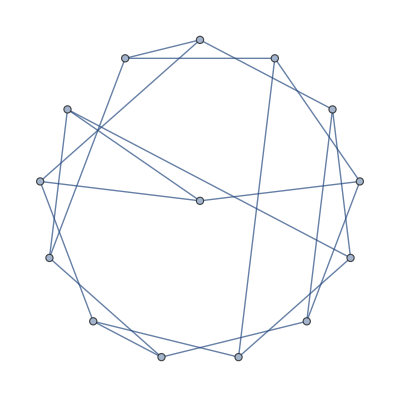

```mathematica
finalGraph = Graph[edges, GraphLayout->"StarEmbedding"]
```

```mathematica
ImageCollage[{
	7-> Image[img],
	Image[Column[{Image[highlightedVertices],
	Image[highlightedParallelograms],
	Image[highlightedEdges]}]],
	7-> Image[finalGraph]
}, Background->White
]
```

```mathematica
Rasterize[Row[{Image[img,ImageSize->240],Image[column,ImageSize->80],Image[fGraph,ImageSize->240]}]]
```

-Graphics-

```mathematica
column =Rasterize[Column[{Rasterize[highlightedVertices],
	Rasterize[highlightedParallelograms],
	Rasterize[highlightedEdges]}],RasterSize->2400]
```

-Graphics-

```mathematica
fGraph = Rasterize[finalGraph, RasterSize->3600]
```

-Graphics-